## Evolution of curves

### Initial curves

#### Curves generating function

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];ClearSystemCache[];
```

```mathematica
curgen[num_,width_,height_,kink_,touch_,asymmetrie_,diagonaldistortion_]:=Module[{lo,initialcurve},
Subscript[te, num,0]=0;
initialcurve[u_]:=Exp[asymmetrie (Sin[u]-1)]({width (1-kink Cos[u]^2)(Sin[u]),height  (1-touch Cos[u]^2)(Cos[u])}+diagonaldistortion{Sin[u],Sin[u]});
lo=NIntegrate[Sqrt[D[initialcurve[u], u].D[initialcurve[u], u]],{u,0,2π}];
Subscript[curve, num,0][u_]:=100initialcurve[u]/lo;
ParametricPlot[{Subscript[curve, num,0][u]},{u,0,2π}]];
```

#### 1. curve

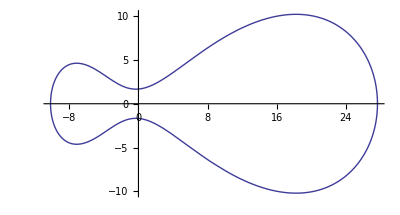

```mathematica
curgen[1,1,1,.4,.9,.5,0]
```

#### 2. curve

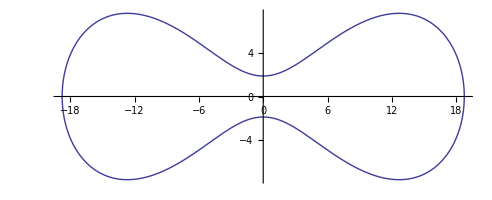

```mathematica
curgen[2,1,1,.4,.9,0,0]
```

#### 3. curve

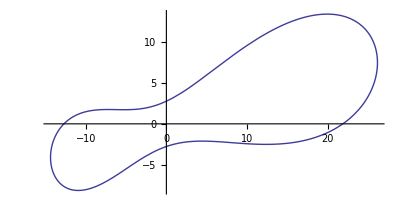

```mathematica
curgen[3,1,1,.4,.8,0.3,.4]
```

#### 4. curve

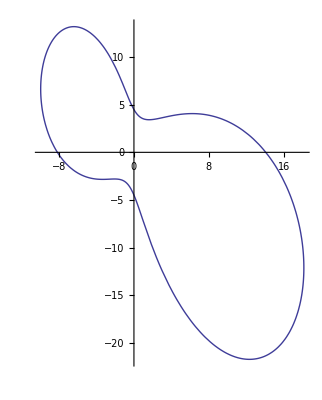

```mathematica
curgen[4,1,1,.4,.8,0.3,-.4]
```

#### 5. curve

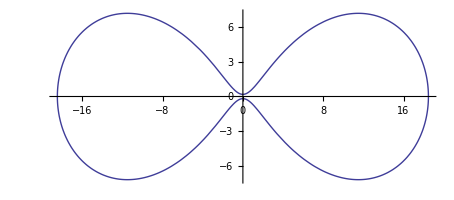

```mathematica
curgen[5,1,1,.7,.99,0,0]
```

#### 6. curve

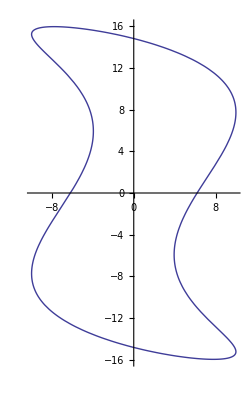

```mathematica
curgen[6,1,1.5,-2,0,0,-.6]
```

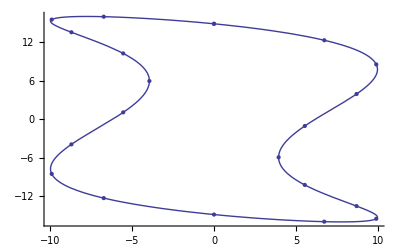

```mathematica
Show[ListPlot[Table[Subscript[curve, 6,0][2Pi i/20],{i,0,20}]],ParametricPlot[Subscript[curve, 6,0][u],{u,0,2Pi}]]
```

### Functions

#### PDE, pbc, length functions

```mathematica
pdeinx =((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[x[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[x[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[x[u,t], t]==0; pdeiny=((D[x[u,t], u])^2+(D[y[u,t], u])^2)D[y[u,t], u,u]-(D[x[u,t], u]D[x[u,t], u,u]+D[y[u,t], u]D[y[u,t], u,u])D[y[u,t], u]-((D[x[u,t], u])^2+(D[y[u,t], u])^2)^2 D[y[u,t], t]==0; 
pbcinx=x[0,t]==x[2π,t] ;
pbciny=y[0,t]==y[2π,t];
clength[num_,step_]:=NIntegrate[Sqrt[(D[Subscript[curve, num,step][u], u]).(D[Subscript[curve, num,step][u], u])],{u,0,2π}];slength[num_,step_]:=NIntegrate[Sqrt[(D[x[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,1]])^2+(D[y[u,Subscript[te, num,step]], u]/.Subscript[solution, num,step][[1,2]])^2],{u,0,2π}];
```

#### Evolution function

```mathematica
flow[num_,step_,tintervall_]:=Module[{time},
Subscript[te, num,step]=Subscript[te, num,step-1]+tintervall;
Subscript[stepstop, num]=step;
time=Timing[Subscript[solution, num,step]=
NDSolve[{ pdeinx, pdeiny,pbcinx,pbciny,D[pbcinx, t],D[pbciny, t],
x[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[1]],
y[u,Subscript[te, num,step-1]]==Subscript[curve, num,step-1][u][[2]]},
{x,y},{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]},
DependentVariables->{x,y},
InterpolationOrder->All,
Method->{"MethodOfLines",
"TemporalVariable"->t,
"SpatialDiscretization"->
{"TensorProductGrid",
DifferenceOrder->6,
MinPoints->100,
StartingPoints->100},
"DifferentiateBoundaryConditions"->True,
Method->Automatic,
Method->Automatic},
WorkingPrecision->MachinePrecision,
AccuracyGoal->Automatic,
PrecisionGoal->Automatic,
InterpolationOrder->Automatic,
SolveDelayed->False];];
If[step==1,
Subscript[sl, num,0]=NIntegrate[Sqrt[(D[x[u,0], u]/.Subscript[solution, num,1][[1,1]])^2+(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])^2],{u,0,2π}];
Subscript[ao, num]=-1/2 NIntegrate[(x[u,0]/.Subscript[solution, num,1][[1,1]])(D[y[u,0], u]/.Subscript[solution, num,1][[1,2]])-(y[u,0]/.Subscript[solution, num,1][[1,2]])( D[x[u,0], u]/.Subscript[solution, num,1][[1,1]]),{u,0,2π}];];
Print[num,". Kurve(",Subscript[ao, num]/(2π),"), ",step,". Evolution:   Laenge Anfangskurve = ",clength[num,step-1]," , Laenge nach Fluss = ",
Subscript[sl, num,step]=slength[num,step]," , Berechnungsdauer = ",time[[1]]]];

fgp[num_,step_,tintervall_]:=(flow[num,step,tintervall];grdplot[num,step]);
```

#### Plotting functions

```mathematica
flowplot[num_,step_]:=ParametricPlot3D[Evaluate[{x[u,t],y[u,t],20t}/. Subscript[solution, num,step]],{u,0,2π},{t,Subscript[te, num,step-1],Subscript[te, num,step]}];
grdplot[num_,step_]:=Module[{xso,yso,grdpts,GridPointPlot},
xso={Subscript[solution, num,step][[1,1]]};
yso={Subscript[solution, num,step][[1,2]]};
GridPointPlot[{x->xif_InterpolatingFunction},{y->yif_InterpolatingFunction}, t_, opts___] := Module[{xgrid = DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[xif][[1]]},
ListPlot[Transpose[{ xif[xgrid, t],yif[xgrid, t]}], opts]];
grdpts=
Map[Length,DifferentialEquations`InterpolatingFunctionAnatomy`InterpolatingFunctionCoordinates[x /. xso]][[1]]-1;
Print["Gitterpunkte von NUMOL: ",grdpts];
Show[
ListPlot[Table[Subscript[curve, num,step-1][2Pi/grdpts i],{i,0,(grdpts-1)}],PlotStyle->{Green,Opacity[.5],PointSize[Medium]}],
GridPointPlot[xso,yso,Subscript[te, num,step-1],PlotStyle->{Red,PointSize[Small]}],
GridPointPlot[xso,yso,Subscript[te, num,step],PlotStyle->{Blue,PointSize[Small]}],
PlotLabel->{Style[Subscript["curve", num,step-1],Green],Style[Subscript[" solution", num,step][Subscript[te, num,step-1]],Red],Style[Subscript[" solution", num,step][Subscript[te, num,step]],Blue]}]];
equiplot[num_,step_]:=Show[
ParametricPlot[{{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]},{u,0,2π}],ListPlot[First[{x[u,Subscript[te, num,step]],y[u,Subscript[te, num,step]]}/. Subscript[solution, num,step]]/. Subscript[ulu, num,step],PlotRange->{{-.15,.15},{-.1,.1}}]];
evoplot[num_]:=Block[{stretch=1},
Show[Table[ParametricPlot3D[{Evaluate[{x[u,t],y[u,t],stretch t}/. Subscript[solution, num,i]],{0,0,0}},{u,0,2π},{t,Subscript[te, num,i-1],Subscript[te, num,i]},PlotPoints->{30,10},Mesh->None],{i,Subscript[stepstop, num],1,-1}],PlotRange->All]];
```

#### Fitting functions

```mathematica
equidist[num_,step_,fitpts_,opts___]:=Module[{length,l,L,usol,time},
Subscript[numberoffitpts, num,step]=fitpts;
length=slength[num,step];
l[i_]:=length i/fitpts;
L[u_?NumberQ]:=NIntegrate[Sqrt[(D[Evaluate[x[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]], p])^2+(D[Evaluate[y[p,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]], p])^2],{p,0,u},opts];
usol[i_]:=FindRoot[L[u]==l[i],{u,0,2Pi}];
time=Timing[Subscript[ulu, num,step]=Table[usol[i],{i,0,fitpts}]];
Print["u-Bestimmungsdauer: ",time[[1]]];];
fit[num_,step_,order_]:=Module[{fitpts,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat,cl},
fitpts=Subscript[numberoffitpts, num,step];
xpts=Table[{2Pi i/fitpts,x[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,1]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
ypts=Table[{2Pi i/fitpts,y[u,Subscript[te, num,step]]/.Subscript[solution, num,step][[1,2]]/.Subscript[ulu, num,step][[i+1]]},{i,0,fitpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
Subscript[curve, num,step][u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};
cl=clength[num,step];
Print[num,". Kurve, ",step,". Fit: Laenge nach Fluss: ",Subscript[sl, num,step]," , Laenge nach Fit: ",cl," , Abweichung: ",Abs[Subscript[sl, num,step]-cl]/Subscript[sl, num,step] 100"%"]]
```

#### Function over entire t-Interval of coordinates, length, area. Plotting functions

```mathematica
Subscript[xevo, num_][u_,t_]:=Piecewise[Table[{x[u,t]/.Subscript[solution, num,i][[1,1]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[yevo, num_][u_,t_]:=Piecewise[Table[{y[u,t]/.Subscript[solution, num,i][[1,2]],Subscript[te, num,i-1]≤t≤Subscript[te, num,i]},{i,1,Subscript[stepstop, num]}],0];
Subscript[length, num_][t_]:=NIntegrate[Sqrt[(D[Subscript[xevo, num][u,t], u])^2+(D[Subscript[yevo, num][u,t], u])^2],{u,0,2π}];
Subscript[area, num_][t_]:=-1/2 NIntegrate[Subscript[xevo, num][u,t] (D[Subscript[yevo, num][u,t], u])-Subscript[yevo, num][u,t]( D[Subscript[xevo, num][u,t], u]),{u,0,2π}];
Subscript[lplot, num_]:=Show[
Plot[{Subscript[length, num][t]},{t,0,Subscript[te, num,Subscript[stepstop, num]]},Epilog->{PointSize[Large],Opacity[0.5],Green,Point[{Subscript[ao, num]/(2 π),0}]}],
ListPlot[Table[{Subscript[te, num,i],Subscript[sl, num,i]},{i,0,Subscript[stepstop, num]}]]];
Subscript[aplot, num_]:=Plot[Subscript[area, num][t],{t,0,Subscript[te, num,Subscript[stepstop, num]]},PlotRange-> Full];
Subscript[isoplot, num_]:=Plot[{Subscript[length, num][t]^2/Subscript[area, num][t],4π},{t,0,Subscript[te, num,Subscript[stepstop, num]]},Epilog->{PointSize[Large],Opacity[0.5],Green,Point[{Subscript[ao, num]/(2 π),4π}]}];
```

### Evolution

#### 1. curve

1. Kurve(73.245), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 82.542 , Berechnungsdauer = 0.088006

Gitterpunkte von NUMOL: 100

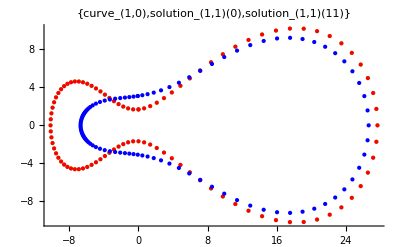

```mathematica
fgp[1,1,11]
```

```mathematica
equidist[1,1,100]
```

u-Bestimmungsdauer: 55.4835

```mathematica
fit[1,1,15];
```

1. Kurve, 1. Fit: Laenge nach Fluss: 82.542 , Laenge nach Fit: 82.5368 , Abweichung: 0.00630502 %

1. Kurve(73.245), 2. Evolution:   Laenge Anfangskurve = 82.5368 , Laenge nach Fluss = 66.5901 , Berechnungsdauer = 0.116007

Gitterpunkte von NUMOL: 100

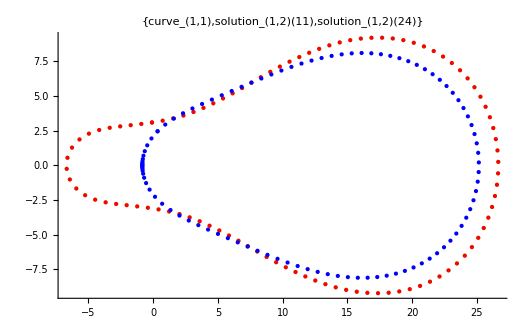

```mathematica
flow[1,2,13];grdplot[1,2]
```

```mathematica
equidist[1,2,90]
```

u-Bestimmungsdauer: 55.1874

```mathematica
fit[1,2,10]
```

1. Kurve, 2. Fit: Laenge nach Fluss: 66.5901 , Laenge nach Fit: 66.5849 , Abweichung: 0.0078047 %

1. Kurve(73.245), 3. Evolution:   Laenge Anfangskurve = 66.5849 , Laenge nach Fluss = 27.0555 , Berechnungsdauer = 0.124007

Gitterpunkte von NUMOL: 100

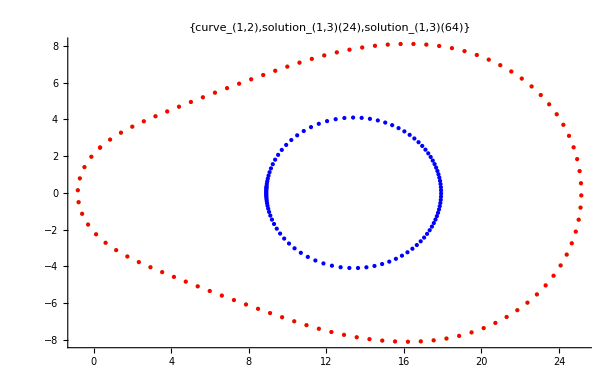

```mathematica
flow[1,3,40];grdplot[1,3]
```

u-Bestimmungsdauer: 53.8434

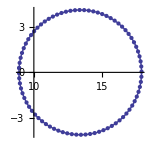

```mathematica
equidist[1,3,80];equiplot[1,3]
```

```mathematica
fit[1,3,3]
```

1. Kurve, 3. Fit: Laenge nach Fluss: 27.0555 , Laenge nach Fit: 27.0556 , Abweichung: 0.000365511 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 18.3538 at t = 72. in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

1. Kurve(73.245), 4. Evolution:   Laenge Anfangskurve = 27.0556 , Laenge nach Fluss = 9.84914 , Berechnungsdauer = 0.092005

Gitterpunkte von NUMOL: 100

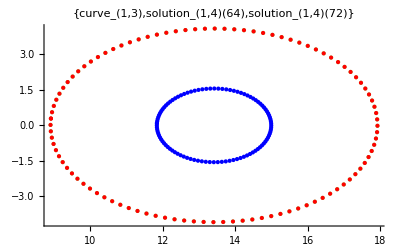

```mathematica
flow[1,4,8];grdplot[1,4]
```

```mathematica
equidist[1,4,50];
```

u-Bestimmungsdauer: 22.2494

```mathematica
fit[1,4,2]
```

1. Kurve, 4. Fit: Laenge nach Fluss: 9.84914 , Laenge nach Fit: 9.84925 , Abweichung: 0.00111477 %

NDSolve::eerr: Warning: Scaled local spatial error estimate of 52.0378 at t = 73.2 in the direction of independent variable u is much greater than prescribed error tolerance. Grid spacing with 101 points may be too large to achieve the desired accuracy or precision.  A singularity may have formed or you may want to specify a smaller grid spacing using the MaxStepSize or MinPoints method options.

1. Kurve(73.245), 5. Evolution:   Laenge Anfangskurve = 9.84925 , Laenge nach Fluss = 1.4367 , Berechnungsdauer = 0.076005

Gitterpunkte von NUMOL: 100

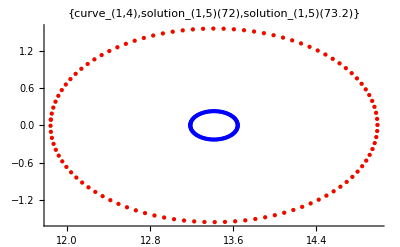

```mathematica
flow[1,5,1.2];grdplot[1,5]
```

```mathematica
equidist[1,5,40]
```

u-Bestimmungsdauer: 17.5211

```mathematica
fit[1,5,1]
```

1. Kurve, 5. Fit: Laenge nach Fluss: 1.4367 , Laenge nach Fit: 1.43671 , Abweichung: 0.0000620341 %

1. Kurve(73.245), 6. Evolution:   Laenge Anfangskurve = 1.43671 , Laenge nach Fluss = 0.692984 , Berechnungsdauer = 0.044003

Gitterpunkte von NUMOL: 100

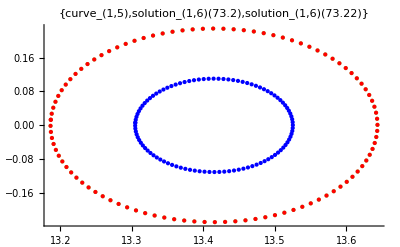

```mathematica
flow[1,6,.02];grdplot[1,6]
```

```mathematica
equidist[1,6,20]
```

u-Bestimmungsdauer: 6.19239

```mathematica
fit[1,6,1]
```

1. Kurve, 6. Fit: Laenge nach Fluss: 0.692984 , Laenge nach Fit: 0.692984 , Abweichung: 0.0000126138 %

1. Kurve(73.245), 7. Evolution:   Laenge Anfangskurve = 0.692984 , Laenge nach Fluss = 0.403782 , Berechnungsdauer = 0.048003

Gitterpunkte von NUMOL: 100

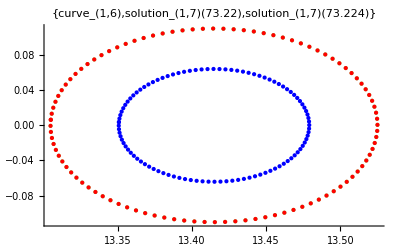

```mathematica
flow[1,7,.004];grdplot[1,7]
```

```mathematica
equidist[1,7,20]
```

u-Bestimmungsdauer: 6.4004

```mathematica
fit[1,7,1]
```

1. Kurve, 7. Fit: Laenge nach Fluss: 0.403782 , Laenge nach Fit: 0.403782 , Abweichung: 5.83657×10^-6 %

1. Kurve(73.245), 8. Evolution:   Laenge Anfangskurve = 0.403782 , Laenge nach Fluss = 0.290905 , Berechnungsdauer = 0.044003

Gitterpunkte von NUMOL: 100

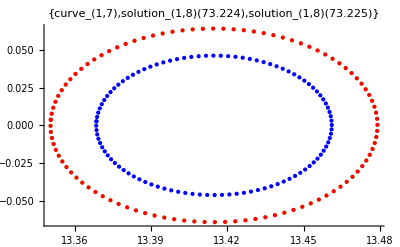

```mathematica
flow[1,8,.00099];grdplot[1,8]
```

```mathematica
equidist[1,8,20]
```

u-Bestimmungsdauer: 5.75636

```mathematica
fit[1,8,1]
```

1. Kurve, 8. Fit: Laenge nach Fluss: 0.290905 , Laenge nach Fit: 0.290905 , Abweichung: 1.95407×10^-6 %

1. Kurve(73.245), 9. Evolution:   Laenge Anfangskurve = 0.290905 , Laenge nach Fluss = 0.24678 , Berechnungsdauer = 0.032002

Gitterpunkte von NUMOL: 100

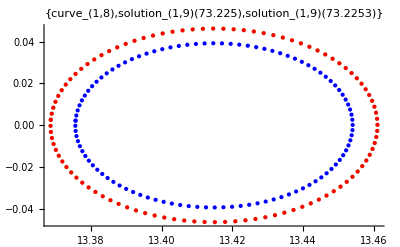

```mathematica
flow[1,9,.0003];grdplot[1,9]
```

#### 2. curve

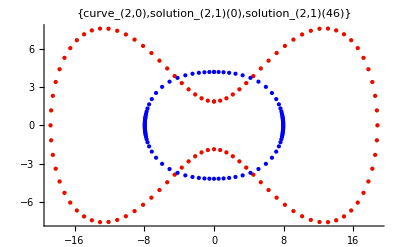

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 39.6962 , Berechnungsdauer = 0.128009

2. Kurve(63.3145), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 39.6962 , Berechnungsdauer = 0.092006

Gitterpunkte von NUMOL: 100

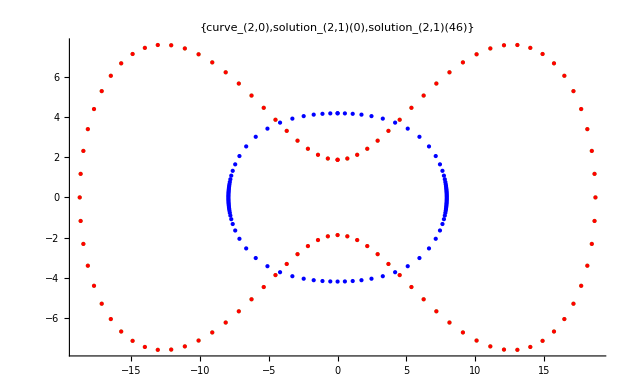

```mathematica
flow[2,1,46];grdplot[2,1]
```

```mathematica
equidist[2,1,60]
```

u-Bestimmungsdauer: 50.0111

u-Bestimmungsdauer: 49.9791

```mathematica
fit[2,1,7]
```

2. Kurve, 1. Fit: Laenge nach Fluss: 39.6962 , Laenge nach Fit: 39.6961 , Abweichung: 0.000409928 %

2. Kurve, 1. Fit: Laenge nach Fluss: 39.6962 , Laenge nach Fit: 39.6961 , Abweichung: 0.000409928 %

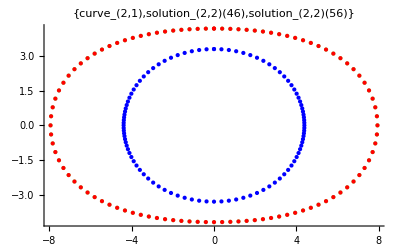

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 2. Evolution:   Laenge Anfangskurve = 39.6961 , Laenge nach Fluss = 24.3847 , Berechnungsdauer = 0.072004

2. Kurve(63.3145), 2. Evolution:   Laenge Anfangskurve = 39.6961 , Laenge nach Fluss = 24.3847 , Berechnungsdauer = 0.076005

Gitterpunkte von NUMOL: 100

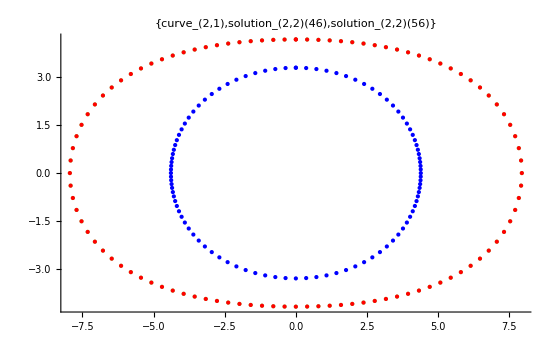

```mathematica
flow[2,2,10];grdplot[2,2]
```

```mathematica
equidist[2,2,50];
```

u-Bestimmungsdauer: 24.5575

u-Bestimmungsdauer: 26.5737

```mathematica
fit[2,2,3]
```

2. Kurve, 2. Fit: Laenge nach Fluss: 24.3847 , Laenge nach Fit: 24.383 , Abweichung: 0.00722406 %

2. Kurve, 2. Fit: Laenge nach Fluss: 24.3847 , Laenge nach Fit: 24.383 , Abweichung: 0.00722406 %

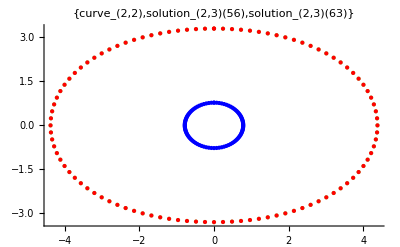

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 3. Evolution:   Laenge Anfangskurve = 24.383 , Laenge nach Fluss = 4.89118 , Berechnungsdauer = 0.064004

2. Kurve(63.3145), 3. Evolution:   Laenge Anfangskurve = 24.383 , Laenge nach Fluss = 4.89118 , Berechnungsdauer = 0.080005

Gitterpunkte von NUMOL: 100

-Graphics-

```mathematica
flow[2,3,7];grdplot[2,3]
```

```mathematica
equidist[2,3,40];
```

u-Bestimmungsdauer: 19.5212

u-Bestimmungsdauer: 19.9492

```mathematica
fit[2,3,1]
```

2. Kurve, 3. Fit: Laenge nach Fluss: 4.89118 , Laenge nach Fit: 4.89094 , Abweichung: 0.00498012 %

2. Kurve, 3. Fit: Laenge nach Fluss: 4.89118 , Laenge nach Fit: 4.89094 , Abweichung: 0.00498012 %

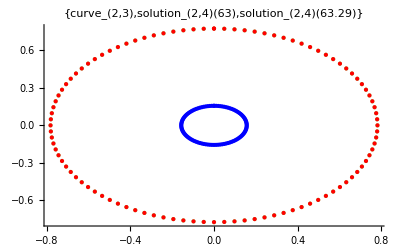

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 4. Evolution:   Laenge Anfangskurve = 4.89094 , Laenge nach Fluss = 0.983948 , Berechnungsdauer = 0.068004

2. Kurve(63.3145), 4. Evolution:   Laenge Anfangskurve = 4.89094 , Laenge nach Fluss = 0.983948 , Berechnungsdauer = 0.072004

Gitterpunkte von NUMOL: 100

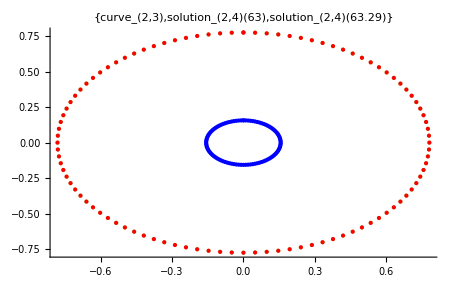

```mathematica
flow[2,4,.29];grdplot[2,4]
```

```mathematica
equidist[2,4,20]
```

u-Bestimmungsdauer: 7.77649

u-Bestimmungsdauer: 7.85249

```mathematica
fit[2,4,1]
```

2. Kurve, 4. Fit: Laenge nach Fluss: 0.983948 , Laenge nach Fit: 0.983946 , Abweichung: 0.000204101 %

2. Kurve, 4. Fit: Laenge nach Fluss: 0.983948 , Laenge nach Fit: 0.983946 , Abweichung: 0.000204101 %

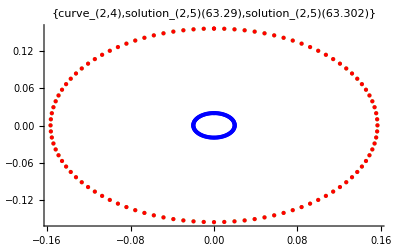

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 5. Evolution:   Laenge Anfangskurve = 0.983946 , Laenge nach Fluss = 0.124682 , Berechnungsdauer = 0.080005

2. Kurve(63.3145), 5. Evolution:   Laenge Anfangskurve = 0.983946 , Laenge nach Fluss = 0.124682 , Berechnungsdauer = 0.088005

Gitterpunkte von NUMOL: 100

-Graphics-

```mathematica
flow[2,5,.012];grdplot[2,5]
```

```mathematica
equidist[2,5,20]
```

u-Bestimmungsdauer: 6.71642

u-Bestimmungsdauer: 6.62842

```mathematica
fit[2,5,1]
```

2. Kurve, 5. Fit: Laenge nach Fluss: 0.124682 , Laenge nach Fit: 0.124682 , Abweichung: 3.08267×10^-6 %

2. Kurve, 5. Fit: Laenge nach Fluss: 0.124682 , Laenge nach Fit: 0.124682 , Abweichung: 3.08267×10^-6 %

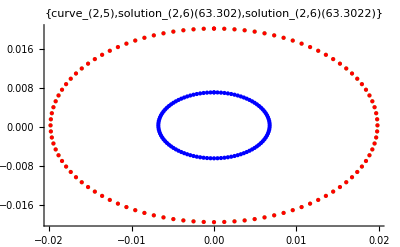

Gitterpunkte von NUMOL: 100

2. Kurve(63.3145), 6. Evolution:   Laenge Anfangskurve = 0.124682 , Laenge nach Fluss = 0.0424677 , Berechnungsdauer = 0.040002

2. Kurve(63.3145), 6. Evolution:   Laenge Anfangskurve = 0.124682 , Laenge nach Fluss = 0.0424677 , Berechnungsdauer = 0.040003

Gitterpunkte von NUMOL: 100

-Graphics-

```mathematica
flow[2,6,.00017];grdplot[2,6]
```

#### 3. curve

3. Kurve(63.3345), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 80.3068 , Berechnungsdauer = 0.076005

Gitterpunkte von NUMOL: 100

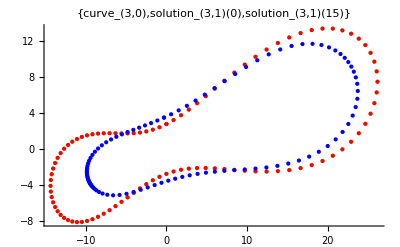

```mathematica
fgp[3,1,15]
```

```mathematica
equidist[3,1,100]
```

u-Bestimmungsdauer: 52.9873

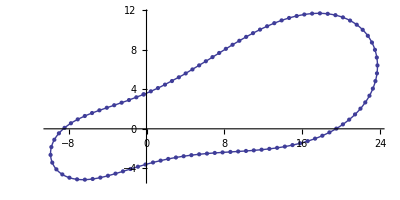

```mathematica
equiplot[3,1]
```

```mathematica
fit[3,1,13]
```

3. Kurve, 1. Fit: Laenge nach Fluss: 80.3068 , Laenge nach Fit: 80.3023 , Abweichung: 0.00567079 %

3. Kurve(63.3345), 2. Evolution:   Laenge Anfangskurve = 80.3023 , Laenge nach Fluss = 64.8968 , Berechnungsdauer = 0.140009

Gitterpunkte von NUMOL: 100

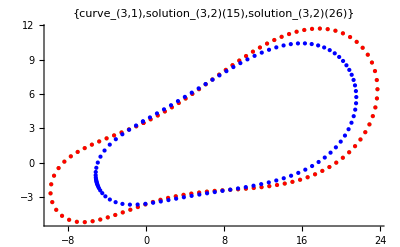

```mathematica
fgp[3,2,11]
```

```mathematica
equidist[3,2,100]
```

u-Bestimmungsdauer: 61.3358

```mathematica
fit[3,2,11]
```

3. Kurve, 2. Fit: Laenge nach Fluss: 64.8968 , Laenge nach Fit: 64.8916 , Abweichung: 0.00810146 %

3. Kurve(63.3345), 3. Evolution:   Laenge Anfangskurve = 64.8916 , Laenge nach Fluss = 49.0602 , Berechnungsdauer = 0.092006

Gitterpunkte von NUMOL: 100

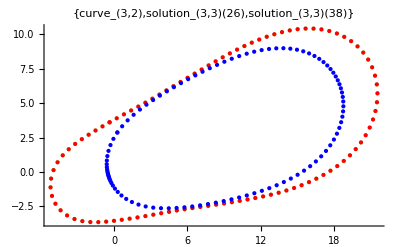

```mathematica
fgp[3,3,12]
```

```mathematica
equidist[3,3,80]
```

u-Bestimmungsdauer: 47.891

```mathematica
fit[3,3,8]
```

3. Kurve, 3. Fit: Laenge nach Fluss: 49.0602 , Laenge nach Fit: 49.0573 , Abweichung: 0.00572286 %

3. Kurve(63.3345), 4. Evolution:   Laenge Anfangskurve = 49.0573 , Laenge nach Fluss = 20.6153 , Berechnungsdauer = 0.088006

Gitterpunkte von NUMOL: 100

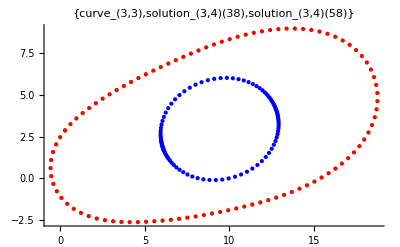

```mathematica
fgp[3,4,20]
```

```mathematica
equidist[3,4,60]
```

u-Bestimmungsdauer: 38.8744

```mathematica
fit[3,4,3]
```

3. Kurve, 4. Fit: Laenge nach Fluss: 20.6153 , Laenge nach Fit: 20.6154 , Abweichung: 0.00036568 %

3. Kurve(63.3345), 5. Evolution:   Laenge Anfangskurve = 20.6154 , Laenge nach Fluss = 7.03012 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

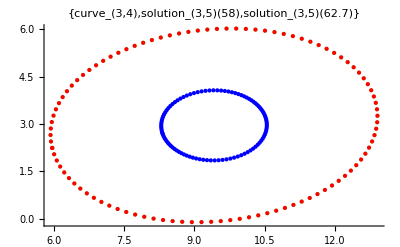

```mathematica
fgp[3,5,4.7]
```

```mathematica
equidist[3,5,40]
```

u-Bestimmungsdauer: 19.1692

```mathematica
fit[3,5,1]
```

3. Kurve, 5. Fit: Laenge nach Fluss: 7.03012 , Laenge nach Fit: 7.03023 , Abweichung: 0.00165901 %

3. Kurve(63.3345), 6. Evolution:   Laenge Anfangskurve = 7.03023 , Laenge nach Fluss = 3.00947 , Berechnungsdauer = 0.040003

Gitterpunkte von NUMOL: 100

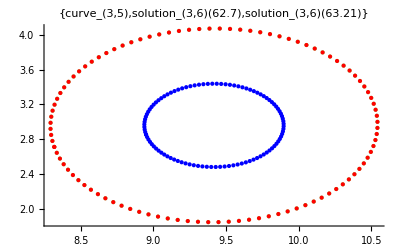

```mathematica
fgp[3,6,.51]
```

```mathematica
equidist[3,6,20]
```

u-Bestimmungsdauer: 8.06451

```mathematica
fit[3,6,1]
```

3. Kurve, 6. Fit: Laenge nach Fluss: 3.00947 , Laenge nach Fit: 3.00951 , Abweichung: 0.00144413 %

3. Kurve(63.3345), 7. Evolution:   Laenge Anfangskurve = 3.00951 , Laenge nach Fluss = 1.06485 , Berechnungsdauer = 0.048002

Gitterpunkte von NUMOL: 100

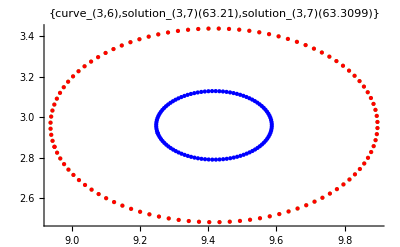

```mathematica
fgp[3,7,.0999]
```

```mathematica
equidist[3,7,20]
```

u-Bestimmungsdauer: 7.55247

```mathematica
fit[3,7,1]
```

3. Kurve, 7. Fit: Laenge nach Fluss: 1.06485 , Laenge nach Fit: 1.06485 , Abweichung: 0.000120902 %

```mathematica
fgp[3,7,.0999]
```

3. Kurve(63.3345), 7. Evolution:   Laenge Anfangskurve = 3.00951 , Laenge nach Fluss = 1.06485 , Berechnungsdauer = 0.044003

Gitterpunkte von NUMOL: 100

-Graphics-

#### 4. curve

4. Kurve(74.6236), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 70.241 , Berechnungsdauer = 0.144009

Gitterpunkte von NUMOL: 100

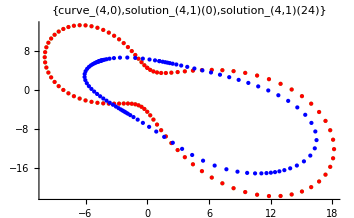

```mathematica
fgp[4,1,24]
```

```mathematica
equidist[4,1,100]
```

u-Bestimmungsdauer: 81.4571

```mathematica
fit[4,1,10]
```

4. Kurve, 1. Fit: Laenge nach Fluss: 70.241 , Laenge nach Fit: 70.2401 , Abweichung: 0.00120619 %

4. Kurve(74.6236), 2. Evolution:   Laenge Anfangskurve = 70.2401 , Laenge nach Fluss = 29.1081 , Berechnungsdauer = 0.128008

Gitterpunkte von NUMOL: 100

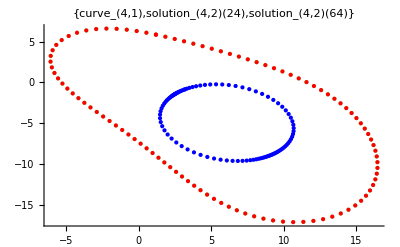

```mathematica
fgp[4,2,40]
```

```mathematica
equidist[4,2,60]
```

u-Bestimmungsdauer: 41.5986

```mathematica
fit[4,2,3]
```

4. Kurve, 2. Fit: Laenge nach Fluss: 29.1081 , Laenge nach Fit: 29.1082 , Abweichung: 0.000294101 %

4. Kurve(74.6236), 3. Evolution:   Laenge Anfangskurve = 29.1082 , Laenge nach Fluss = 4.96809 , Berechnungsdauer = 0.076005

Gitterpunkte von NUMOL: 100

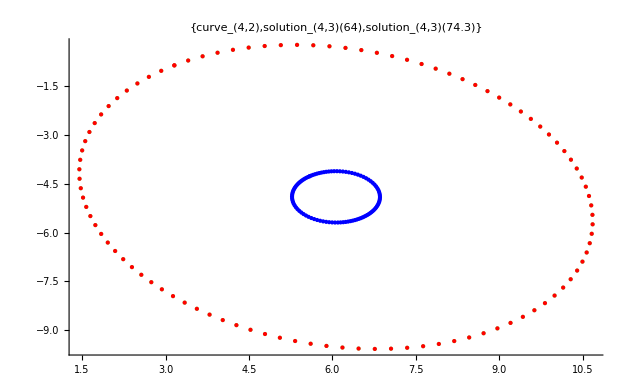

```mathematica
fgp[4,3,10.3]
```

```mathematica
equidist[4,3,40]
```

u-Bestimmungsdauer: 19.7012

```mathematica
fit[4,3,3]
```

4. Kurve, 3. Fit: Laenge nach Fluss: 4.96809 , Laenge nach Fit: 4.96808 , Abweichung: 0.000239402 %

4. Kurve(74.6236), 4. Evolution:   Laenge Anfangskurve = 4.96808 , Laenge nach Fluss = 1.29305 , Berechnungsdauer = 0.048003

Gitterpunkte von NUMOL: 100

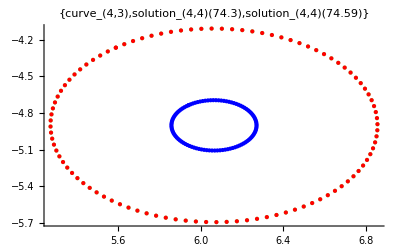

```mathematica
fgp[4,4,.29]
```

```mathematica
equidist[4,4,40]
```

u-Bestimmungsdauer: 14.7729

```mathematica
fit[4,4,1]
```

4. Kurve, 4. Fit: Laenge nach Fluss: 1.29305 , Laenge nach Fit: 1.29305 , Abweichung: 0.0000787001 %

4. Kurve(74.6236), 5. Evolution:   Laenge Anfangskurve = 1.29305 , Laenge nach Fluss = 0.182754 , Berechnungsdauer = 0.044003

Gitterpunkte von NUMOL: 100

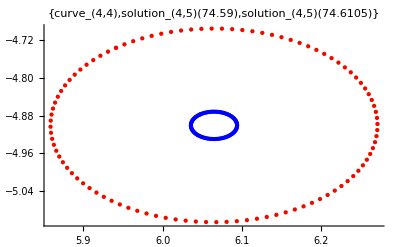

```mathematica
fgp[4,5,.0205]
```

```mathematica
equidist[4,5,20]
```

u-Bestimmungsdauer: 7.32046

```mathematica
fit[4,5,1]
```

4. Kurve, 5. Fit: Laenge nach Fluss: 0.182754 , Laenge nach Fit: 0.182754 , Abweichung: 0.0000487377 %

4. Kurve(74.6236), 6. Evolution:   Laenge Anfangskurve = 0.182754 , Laenge nach Fluss = 0.0614145 , Berechnungsdauer = 0.036003

Gitterpunkte von NUMOL: 100

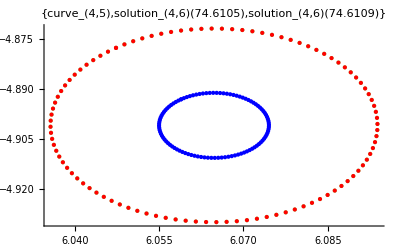

```mathematica
fgp[4,6,.00037]
```

#### 5. curve

Caution! 200 gridpoints used.

5. Kurve(58.4327), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 34.5412 , Berechnungsdauer = 0.136009

Gitterpunkte von NUMOL: 100

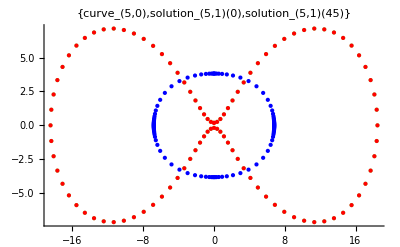

```mathematica
fgp[5,1,45]
```

```mathematica
equidist[5,1,80]
```

u-Bestimmungsdauer: 66.7402

```mathematica
fit[5,1,8]
```

5. Kurve, 1. Fit: Laenge nach Fluss: 34.5412 , Laenge nach Fit: 34.5411 , Abweichung: 0.000180248 %

5. Kurve(58.4327), 2. Evolution:   Laenge Anfangskurve = 34.5411 , Laenge nach Fluss = 13.8888 , Berechnungsdauer = 0.080005

Gitterpunkte von NUMOL: 100

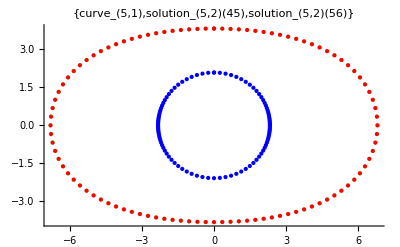

```mathematica
fgp[5,2,11]
```

```mathematica
equidist[5,2,40]
```

u-Bestimmungsdauer: 22.1654

```mathematica
fit[5,2,5]
```

5. Kurve, 2. Fit: Laenge nach Fluss: 13.8888 , Laenge nach Fit: 13.8888 , Abweichung: 0.0000160481 %

5. Kurve(58.4327), 3. Evolution:   Laenge Anfangskurve = 13.8888 , Laenge nach Fluss = 5.07538 , Berechnungsdauer = 0.052003

Gitterpunkte von NUMOL: 100

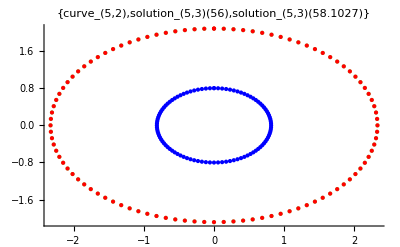

```mathematica
fgp[5,3,2.1027]
```

```mathematica
equidist[5,3,40]
```

u-Bestimmungsdauer: 17.7011

```mathematica
fit[5,3,3]
```

5. Kurve, 3. Fit: Laenge nach Fluss: 5.07538 , Laenge nach Fit: 5.07538 , Abweichung: 0.000014717 %

5. Kurve(58.4327), 4. Evolution:   Laenge Anfangskurve = 5.07538 , Laenge nach Fluss = 1.42078 , Berechnungsdauer = 0.068004

Gitterpunkte von NUMOL: 100

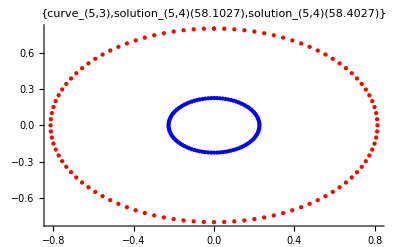

```mathematica
fgp[5,4,.3]
```

```mathematica
equidist[5,4,24]
```

u-Bestimmungsdauer: 9.42059

```mathematica
fit[5,4,3]
```

5. Kurve, 4. Fit: Laenge nach Fluss: 1.42078 , Laenge nach Fit: 1.42078 , Abweichung: 0.0000378263 %

5. Kurve(58.4327), 5. Evolution:   Laenge Anfangskurve = 1.42078 , Laenge nach Fluss = 0.526419 , Berechnungsdauer = 0.056004

Gitterpunkte von NUMOL: 100

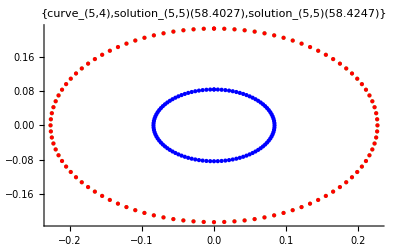

```mathematica
fgp[5,5,.02198]
```

#### 6. curve

6. Kurve(65.7256), 1. Evolution:   Laenge Anfangskurve = 100. , Laenge nach Fluss = 99.6106 , Berechnungsdauer = 0.020001

Gitterpunkte von NUMOL: 100

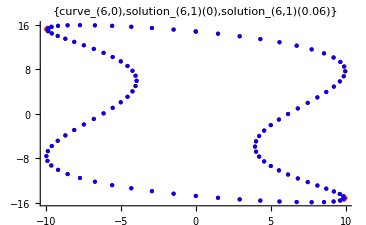

```mathematica
fgp[6,1,.06]
```

```mathematica
equidist[6,1,100]
```

u-Bestimmungsdauer: 41.1586

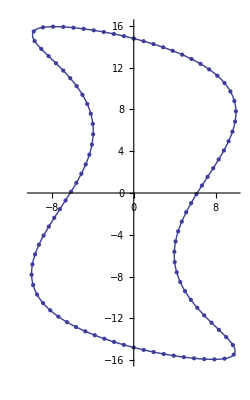

```mathematica
equiplot[6,1]
```

```mathematica
fit[6,1,15]
```

6. Kurve, 1. Fit: Laenge nach Fluss: 99.6106 , Laenge nach Fit: 98.8709 , Abweichung: 0.742609 %

6. Kurve(65.7256), 2. Evolution:   Laenge Anfangskurve = 98.8709 , Laenge nach Fluss = 97.029 , Berechnungsdauer = 0.056004

Gitterpunkte von NUMOL: 100

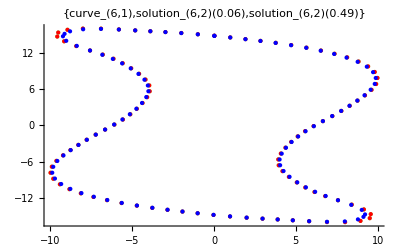

```mathematica
fgp[6,2,.43]
```

```mathematica
equidist[6,2,100]
```

u-Bestimmungsdauer: 38.0464

```mathematica
fit[6,2,15]
```

6. Kurve, 2. Fit: Laenge nach Fluss: 97.029 , Laenge nach Fit: 96.6999 , Abweichung: 0.339165 %

6. Kurve(65.7256), 3. Evolution:   Laenge Anfangskurve = 96.6999 , Laenge nach Fluss = 87.2118 , Berechnungsdauer = 0.084005

Gitterpunkte von NUMOL: 100

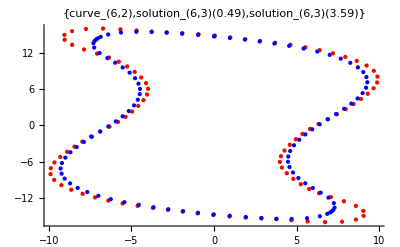

```mathematica
fgp[6,3,3.1]
```

```mathematica
equidist[6,3,100]
```

u-Bestimmungsdauer: 53.1313

```mathematica
fit[6,3,15]
```

6. Kurve, 3. Fit: Laenge nach Fluss: 87.2118 , Laenge nach Fit: 87.1701 , Abweichung: 0.047817 %

6. Kurve(65.7256), 4. Evolution:   Laenge Anfangskurve = 87.1701 , Laenge nach Fluss = 39.4827 , Berechnungsdauer = 0.208012

Gitterpunkte von NUMOL: 100

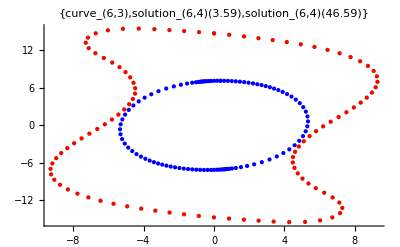

```mathematica
fgp[6,4,43]
```

```mathematica
equidist[6,4,80]
```

u-Bestimmungsdauer: 62.1199

```mathematica
fit[6,4,4]
```

6. Kurve, 4. Fit: Laenge nach Fluss: 39.4827 , Laenge nach Fit: 39.4795 , Abweichung: 0.00819267 %

6. Kurve(65.7256), 5. Evolution:   Laenge Anfangskurve = 39.4795 , Laenge nach Fluss = 15.5876 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

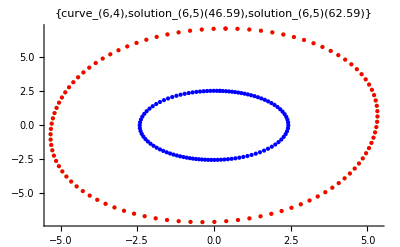

```mathematica
fgp[6,5,16]
```

```mathematica
equidist[6,5,50]
```

u-Bestimmungsdauer: 24.1015

```mathematica
fit[6,5,3]
```

6. Kurve, 5. Fit: Laenge nach Fluss: 15.5876 , Laenge nach Fit: 15.5876 , Abweichung: 0.00013792 %

6. Kurve(65.7256), 6. Evolution:   Laenge Anfangskurve = 15.5876 , Laenge nach Fluss = 6.09522 , Berechnungsdauer = 0.064004

Gitterpunkte von NUMOL: 100

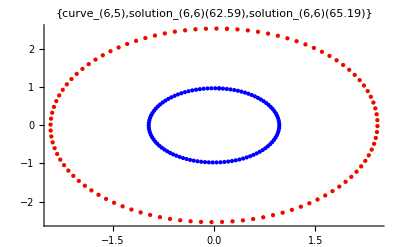

```mathematica
fgp[6,6,2.6]
```

```mathematica
equidist[6,6,20]
```

u-Bestimmungsdauer: 8.38052

```mathematica
fit[6,6,2]
```

6. Kurve, 6. Fit: Laenge nach Fluss: 6.09522 , Laenge nach Fit: 6.09541 , Abweichung: 0.00318842 %

6. Kurve(65.7256), 7. Evolution:   Laenge Anfangskurve = 6.09541 , Laenge nach Fluss = 1.52963 , Berechnungsdauer = 0.060004

Gitterpunkte von NUMOL: 100

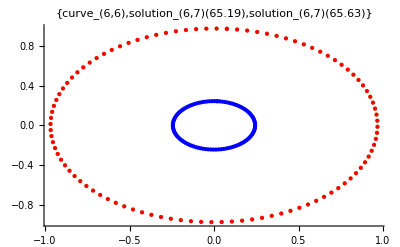

```mathematica
fgp[6,7,.44]
```

```mathematica
equidist[6,7,20]
```

u-Bestimmungsdauer: 7.76048

```mathematica
fit[6,7,1]
```

6. Kurve, 7. Fit: Laenge nach Fluss: 1.52963 , Laenge nach Fit: 1.52963 , Abweichung: 0.000199684 %

6. Kurve(65.7256), 8. Evolution:   Laenge Anfangskurve = 1.52963 , Laenge nach Fluss = 0.497564 , Berechnungsdauer = 0.048003

Gitterpunkte von NUMOL: 100

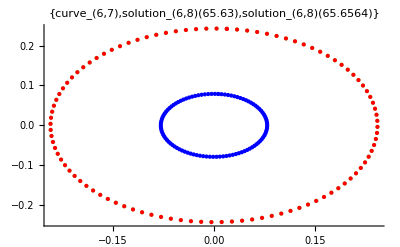

```mathematica
fgp[6,8,.0264]
```

```mathematica
equidist[6,8,10]
```

u-Bestimmungsdauer: 3.57622

```mathematica
fit[6,8,1]
```

6. Kurve, 8. Fit: Laenge nach Fluss: 0.497564 , Laenge nach Fit: 0.497564 , Abweichung: 0.000128033 %

6. Kurve(65.7256), 9. Evolution:   Laenge Anfangskurve = 0.497564 , Laenge nach Fluss = 0.0879921 , Berechnungsdauer = 0.068004

Gitterpunkte von NUMOL: 100

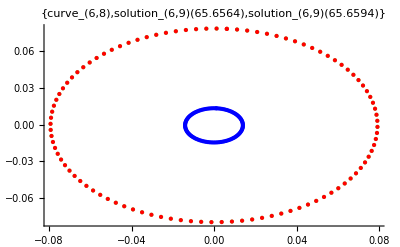

```mathematica
fgp[6,9,.003]
```

#### Evolution plots

```mathematica
evoplot[6]
```

-Graphics3D-

### Evolution plots of lenght, area and isoperimetric ratio

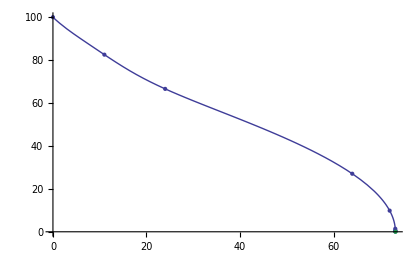

```mathematica
Subscript[lplot, 1]
```

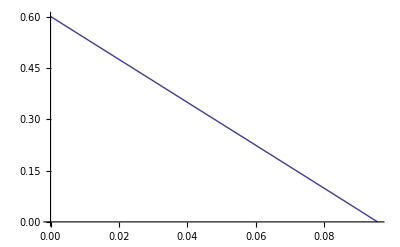

```mathematica
Subscript[aplot, 1]
```

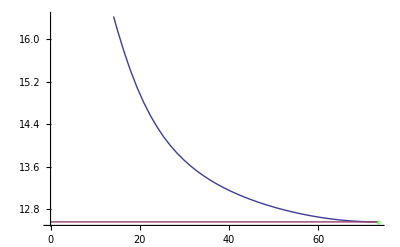

```mathematica
Subscript[isoplot, 1]
```

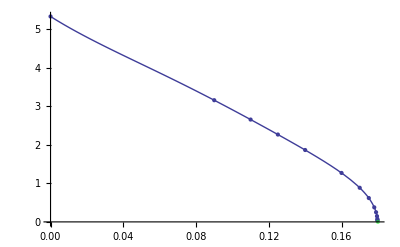

```mathematica
Subscript[lplot, 2]
```

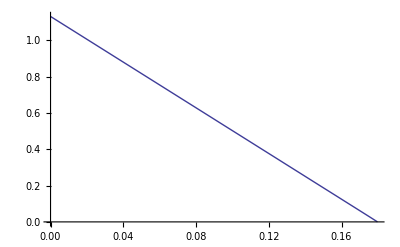

```mathematica
Subscript[aplot, 2]
```

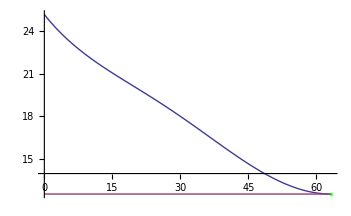

```mathematica
Subscript[isoplot, 2]
```

### Partition function

```mathematica
tmax=1/2 (L/(2Pi))^2/.L->100//N
```

126.651

```mathematica
Subscript[isoint, 1]=Interpolation[Block[{num=1,datapts=20},Join[Table[{i/datapts Subscript[te, num,Subscript[stepstop, num]],Subscript[length, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]^2/Subscript[area, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]},{i,0,datapts}],Table[{Subscript[te, num,Subscript[stepstop, num]]+i/datapts (tmax -Subscript[te, num,Subscript[stepstop, num]]),4 Pi},{i,1,datapts}]]]]
```

InterpolatingFunction[{{0.,126.651}},<>]

```mathematica
Subscript[isoint, 2]=Interpolation[Block[{num=2,datapts=20},Join[Table[{i/datapts Subscript[te, num,Subscript[stepstop, num]],Subscript[length, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]^2/Subscript[area, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]},{i,0,datapts}],Table[{Subscript[te, num,Subscript[stepstop, num]]+i/datapts (tmax -Subscript[te, num,Subscript[stepstop, num]]),4 Pi},{i,1,datapts}]]]]
```

InterpolatingFunction[{{0.,126.651}},<>]

```mathematica
isofit[num_,datapts_,order_]:=Fit[Join[Table[{i/datapts Subscript[te, num,Subscript[stepstop, num]],Subscript[length, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]^2/Subscript[area, num][i/datapts Subscript[te, num,Subscript[stepstop, num]]]},{i,0,datapts}],Table[{Subscript[te, num,Subscript[stepstop, num]]+i/datapts (tmax -Subscript[te, num,Subscript[stepstop, num]]),4 Pi},{i,1,datapts}]],Table[t^i,{i,0,order}],t]
```

```mathematica
Do[Subscript[iso, num]=isofit[num,50,10],{num,1,6}]
```

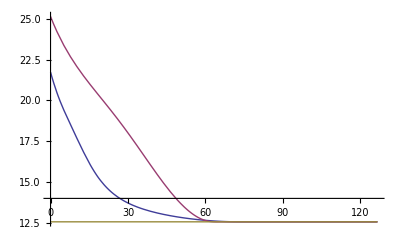

```mathematica
Plot[{Subscript[isoint, 1][t],Subscript[isoint, 2][t],4Pi},{t,0,tmax},PlotRange->Full]
```

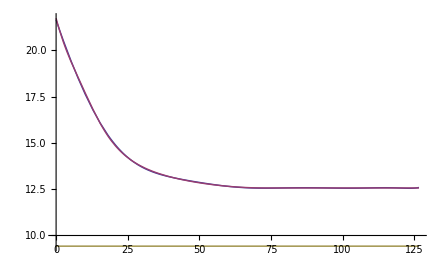

```mathematica
Plot[{Subscript[iso, 1],Subscript[isoint, 1][t],3Pi},{t,0,tmax},PlotRange->Full]
```

```mathematica
noc=2;
z=Sum[Exp[-Subscript[iso, num](1+Subscript[c, num][t])],{num,1,noc}];
pde=Evaluate[D[z, t]] ==0;
bc=Table[Subscript[c, num][0]==0,{num,1,noc}];
```

```mathematica
Join[{pde},bc]
```

{ⅇ^((-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) (1+c_1[t])) ((0.460018-0.0165174 t+0.00122453 t^2-0.000130445 t^3+6.15157×10^-6 t^4-1.49434×10^-7 t^5+2.05557×10^-9 t^6-1.62291×10^-11 t^7+6.86804×10^-14 t^8-1.20881×10^-16 t^9) (1+c_1[t])+(-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) c_1'[t])+ⅇ^((-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) (1+c_2[t])) ((0.340811+0.00192456 t-0.00281651 t^2+0.000221027 t^3-7.18086×10^-6 t^4+1.17294×10^-7 t^5-9.92789×10^-10 t^6+3.80887×10^-12 t^7-1.81853×10^-15 t^8-1.81608×10^-17 t^9) (1+c_2[t])+(-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) c_2'[t])==0,c_1[0]==0,c_2[0]==0}

```mathematica
zsol=DSolve[Join[{pde},bc],Table[Subscript[c, num][t],{num,1,noc}],t]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[{ⅇ^((-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) (1+c_1[t])) ((0.460018-0.0165174 t+0.00122453 t^2-0.000130445 t^3+6.15157×10^-6 t^4-1.49434×10^-7 t^5+2.05557×10^-9 t^6-1.62291×10^-11 t^7+6.86804×10^-14 t^8-1.20881×10^-16 t^9) (1+c_1[t])+(-21.6388+0.460018 t-0.0082587 t^2+0.000408177 t^3-0.0000326113 t^4+1.23031×10^-6 t^5-2.49057×10^-8 t^6+2.93653×10^-10 t^7-2.02864×10^-12 t^8+7.63116×10^-15 t^9-1.20881×10^-17 t^10) c_1'[t])+ⅇ^((-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) (1+c_2[t])) ((0.340811+0.00192456 t-0.00281651 t^2+0.000221027 t^3-7.18086×10^-6 t^4+1.17294×10^-7 t^5-9.92789×10^-10 t^6+3.80887×10^-12 t^7-1.81853×10^-15 t^8-1.81608×10^-17 t^9) (1+c_2[t])+(-25.0838+0.340811 t+0.000962282 t^2-0.000938838 t^3+0.0000552568 t^4-1.43617×10^-6 t^5+1.9549×10^-8 t^6-1.41827×10^-10 t^7+4.76109×10^-13 t^8-2.02059×10^-16 t^9-1.81608×10^-18 t^10) c_2'[t])==0,c_1[0]==0,c_2[0]==0},{c_1[t],c_2[t]},t]

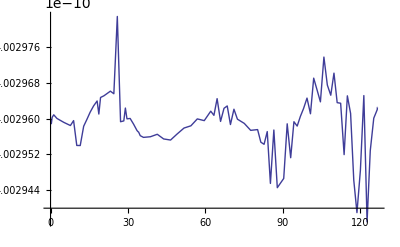

```mathematica
Plot[z/.zsol,{t,0,tmax}]
```